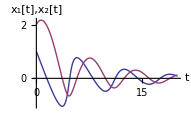

```mathematica
sol=NDSolve[{
x'[t]==-y[t]/(1+y[t]),
y'[t]==x[t]-y[t]/4,
x[0]==1,
y[0]==2},
{x[t],y[t]},{t,0,20}]⟦1⟧;
Plot[{x[t]/.sol,y[t]/.sol},{t,0,20},AxesLabel->{"t","x_1[t],x_2[t]"}]
```

```mathematica
ParametricPlot[{x[t]/.sol,y[t]/.sol},{t,0,20},AxesLabel->{"x_1[t]","x_2[t]"}]
```

-Graphics-

```mathematica
{x[t]/.sol,y[t]/.sol}/.t->3
```

{-0.875609,0.711908}

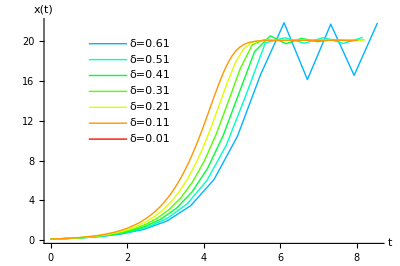

```mathematica
gr={};
For[δ=0.61,δ>0.01,δ=δ-0.1,
x=0.1;
y=10;
t=0;
tf=8;
traj={{t,x}};
While[t<tf,
xn=x+δ((2x y)/(5+y));
yn=y-δ(1/2(2x y)/(5+y));
x=xn;
y=yn;
t=t+δ;
traj=Append[traj,{t,x}];

];
g=ListPlot[traj,Joined->True,PlotRange->All,PlotStyle->Hue[0.9δ]];
gr=Append[gr,g]
];
Show[{
Graphics[Table[
{Text["δ="<>ToString[δ],{2.6,10+16δ}],{Hue[0.9δ],Line[{{1,10+16δ},{2,10+16δ}}]}},
{δ,0.61,0.01,-0.1}]],
gr
},AxesLabel->{"t","x(t)"},Axes->True,AspectRatio->2/3]
```

```mathematica
Solve[(v x y)/(k+y)==0,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0},{y→0}}

```mathematica
FullSimplify[Solve[{(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])==u Subscript[x, 1],γ(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])==u(Subscript[n, 0]-Subscript[x, 2])},{Subscript[x, 1],Subscript[x, 2]}]]
```

{{x_1→0,x_2→n_0},{x_1→((k u)/(u-v)+n_0)/γ,x_2→(k u)/(-u+v)}}

```mathematica
Simplify[((k u)/(u-v)+Subscript[n, 0])/γ==(k u+Subscript[n, 0](u-v))/(γ(u-v))]
```

True

```mathematica
f={(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])-u Subscript[x, 1],γ(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])+u(Subscript[n, 0]-Subscript[x, 2])};
J=FullSimplify[{
{D[f⟦1⟧,Subscript[x, 1]],D[f⟦1⟧,Subscript[x, 2]]},
{D[f⟦2⟧,Subscript[x, 1]],D[f⟦2⟧,Subscript[x, 2]]}
}]/.Subscript[x, 1]->0/.Subscript[x, 2]->Subscript[n, 0];
FullSimplify[J]//MatrixForm
```

(-u+(v n_0)/(k+n_0) | 0
(v γ n_0)/(k+n_0) | -u)

```mathematica
Eigenvalues[J]
```

{-u,-u+(v n_0)/(k+n_0)}

```mathematica
FullSimplify[Solve[{(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])-u Subscript[x, 1]==0,-γ(v Subscript[x, 1] Subscript[x, 2])/(k+Subscript[x, 2])+u(Subscript[n, 0]-Subscript[x, 2])==0},{Subscript[x, 1],Subscript[x, 2]}]]/.{v->1,k->1,γ->1,Subscript[n, 0]->1}
```

{{x_1→0,x_2→1},{x_1→1+u/(-1+u),x_2→u/(1-u)}}

```mathematica
Eigenvalues[A]
```

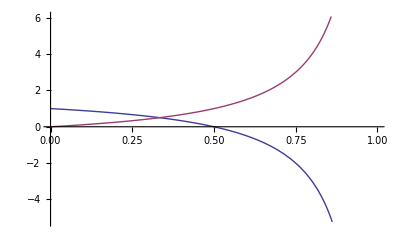

```mathematica
Plot[{1+u/(-1+u),u/(1-u)},{u,0,1}]
```

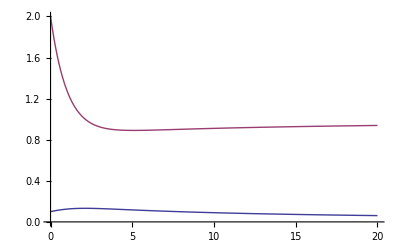

```mathematica
tf=20;
params={v->2,k->1,γ->1,Subscript[n, 0]->1,u->1};
sol=NDSolve[{
Subscript[x, 1]'[t]==(v Subscript[x, 1][t]Subscript[x, 2][t])/(k+Subscript[x, 2][t])-u Subscript[x, 1][t],
Subscript[x, 2]'[t]==-γ(v Subscript[x, 1][t]Subscript[x, 2][t])/(k+Subscript[x, 2][t])+u(Subscript[n, 0]- Subscript[x, 2][t]),
Subscript[x, 1][0]==0.1,Subscript[x, 2][0]==2}/.params,{Subscript[x, 1][t],Subscript[x, 2][t]},{t,0,tf}];
Plot[{Subscript[x, 1][t]/.sol,Subscript[x, 2][t]/.sol},{t,0,tf}]
```